### Init

```mathematica
SetDirectory[NotebookDirectory[]];
string = ReadString["data_en.py"];
lines = Rest[StringSplit[string, "\r\n"]];
clean = StringRiffle[StringReplace[StringDrop[lines,-1], {"senticnet"|"["|"="|"'" ->"", "]" -> "," }], "\n"];
list =ImportString[clean, "CSV"];
stringTrim[s_?StringQ] := StringTrim[s]
stringTrim[any_] := any
listclean =Map[stringTrim, list, {2}];
ruleset = #[[1]]->#[[2;;5]]&/@listclean;
ruleset
```

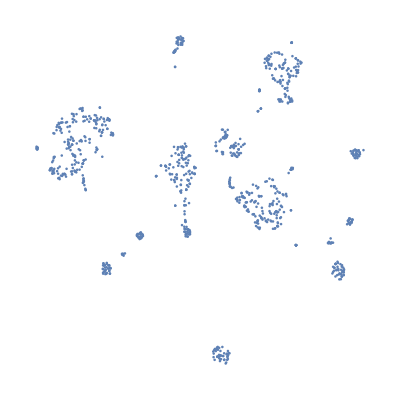

```mathematica
FeatureSpacePlot[Reverse/@RandomSample[ruleset, 50000],LabelingFunction->Tooltip]
```

#### Prepare Data

```mathematica
pleasantnessdata = MapAt[#[[1]]&, MapAt[StringReplace["_" -> " "], ruleset, {All, 1}], {All, 2}];
attentiondata = MapAt[#[[2]]&, MapAt[StringReplace["_" -> " "], ruleset, {All, 1}], {All, 2}];
sensitivitydata = MapAt[#[[3]]&, MapAt[StringReplace["_" -> " "], ruleset, {All, 1}], {All, 2}];
aptitudedata = MapAt[#[[4]]&, MapAt[StringReplace["_" -> " "], ruleset, {All, 1}], {All, 2}];
```

#### Build Predictors

```mathematica
pleasantnessPredictor = Predict[pleasantnessdata];
attentionPredictor = Predict[attentiondata];
sensitivityPredictor = Predict[sensitivitydata];
aptitudePredictor = Predict[aptitudedata];
```

#### Operations

```mathematica
affectSense[text_]:=<|"pleasant"->pleasantnessPredictor[text],"attention"->attentionPredictor[text],"sensitive"->sensitivityPredictor[text],"aptitude"->aptitudePredictor[text]|>
```

```mathematica
affectSense["I am not sad"]
```

<|pleasant→0.070524,attention→0.03249,sensitive→0.0912,aptitude→0.163948|>

```mathematica
affectSense["I am sad not"]
```

<|pleasant→0.070524,attention→0.03249,sensitive→0.0912,aptitude→0.163948|>

```mathematica
affectSense["I am glad a lot I have 32 teeth"]
```

<|pleasant→0.126686,attention→0.121785,sensitive→0.05129,aptitude→0.427241|>

```mathematica
affectSense["I wonder what I have to do next to succced at this"]
```

<|pleasant→0.115456,attention→0.02156,sensitive→0.10587,aptitude→0.148354|>

```mathematica
pleasantnessPredictor
```

PredictorFunction[…]